```mathematica
h=0.1;V[x_]:=x^2
ℒ=-(h^2/(2*0.5))*u''[x]+V[x]*u[x];
```

```mathematica
{vals,funs}=NDEigensystem[ℒ,u[x],{x,-3,3},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9}

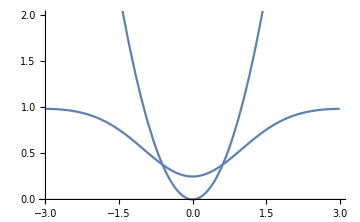

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-3,3}],Plot[V[x],{x,-3,3}],PlotRange->{{-3,3},{0,2}},AxesOrigin->{-3,0},ImageSize->Medium]
```

```mathematica
eigen_qho=Table[h*Sqrt[2/0.5]*(n+0.5),{n,0,10}]
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1}

```mathematica
eigen_mathe=Table[h*2*(n+0.5),{n,0,10}]
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1}